```mathematica
(* assume points are listed in ccw order *)
mlpointfrompair[x1_,x2_]:=Module[{d=Norm[x2-x1],normalvec},
normalvec={{0,1},{-1,0}}.((x2-x1)/d);
(x1+x2)/2+d/2 normalvec
]

mlmakenextlayer[polygon_]:=Table[
mlpointfrompair[polygon[[i]],polygon[[Mod[i+1,Length[polygon],1]]]]
,{i,Length[polygon]}]


mlmakenlayers[init_,n_]:=Module[{current=init},Join[{init},Table[
current=mlmakenextlayer[current]
,{i,n}]]]
```

```mathematica
(* generate random n-gon by perturbing with "r" *)
init[sides_,aa_:1,r_:.1]:=Table[aa({Cos[2π i/sides],Sin[2π i/sides]}+RandomReal[{-r,r},2]),{i,sides}]

rickardeigenvector[om_,sides_]:=Module[{z},
Table[z=om^(i-1);
{Re[z],Im[z]}
,{i,sides}]]
```

```mathematica
tritry=rickardeigenvector[Exp[2π I /9.],9]+.1rickardeigenvector[Exp[6π I /9.],9];
mllayerstri=mlmakenlayers[tritry,300];
```

```mathematica
in7=init[7,1,0.1];
mllayers7=mlmakenlayers[in7,200];
```

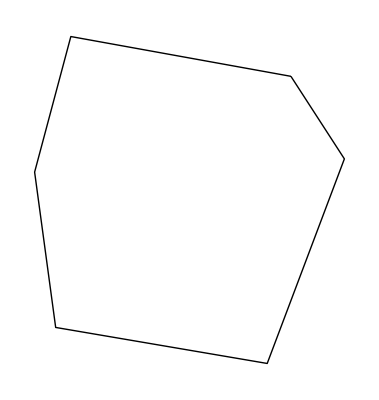

```mathematica
in6=init[6,1,.3];
Graphics[Line[Join[in6,{in6[[1]]}]]]
mllayers6=mlmakenlayers[in6,100];
```

```mathematica
mllayers6[[100]]/10^13
```

{{-2.0951,1.04954},{-1.86954,-0.931927},{-0.480952,-2.1886},{1.92123,-1.76496},{2.57605,1.13906},{-0.0516838,2.69689}}

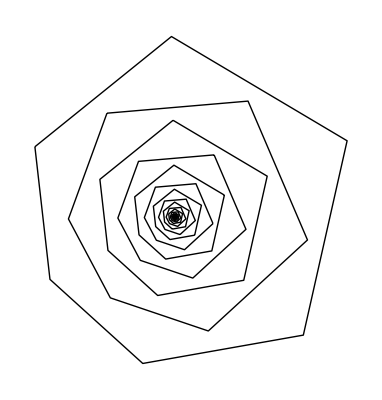

```mathematica
Graphics[Table[Line[Join[mllayers6[[i,All]],{mllayers6[[i,1]]}]],{i,100}]]
```

```mathematica
counterexample={{-2.0951,1.04954},{-1.86954,-0.931927},{-0.480952,-2.1886},{1.92123,-1.76496},{2.57605,1.13906},{-0.0516838,2.69689}};
```

```mathematica
ArcTan[counterexample[[5,1]],counterexample[[5,2]]]
```

0.416326

```mathematica
seed[a_]:=rickardeigenvector[Exp[π I/3.],6]+a rickardeigenvector[I Exp[I π/6.],6];
mllayers6=mlmakenlayers[seed[.17],100];
```

```mathematica
Norm[counterexample[[5]]-counterexample[[6]]]/Norm[counterexample[[1]]-counterexample[[2]]]
ar=a/.FindRoot[Norm[seed[a][[1]]-seed[a][[2]]]/Norm[seed[a][[3]]-seed[a][[4]]]==Norm[counterexample[[5]]-counterexample[[6]]]/Norm[counterexample[[1]]-counterexample[[2]]],{a,0,1}]
```

1.53179

0.142256

```mathematica
mllayersmanip=mllayers7;
Manipulate[Graphics[sidelength=Norm[mllayersmanip[[2i-1,1]]-mllayersmanip[[2i-1,2]]];
{Red,Line[Join[mllayersmanip[[2i-1,All]],{mllayersmanip[[2i-1,1]]}]/sidelength],Blue,
Line[Join[mllayersmanip[[2i,All]],{mllayersmanip[[2i,1]]}]/sidelength]
},PlotLabel->Column[{Style["Step "<>ToString[2i],Blue],Style["Step "<>ToString[2i-1],Red]}],ImageSize->{400,400}],{i,1,Length[mllayersmanip]/2,1}]
```

```mathematica
mllayersmanip=mllayerstri;
trianglelist=Table[Graphics[sidelength=Norm[mllayersmanip[[2i-1,1]]-mllayersmanip[[2i-1,2]]];
{Red,Line[Join[mllayersmanip[[2i-1,All]],{mllayersmanip[[2i-1,1]]}]/sidelength],Blue,
Line[Join[mllayersmanip[[2i,All]],{mllayersmanip[[2i,1]]}]/sidelength]
},PlotLabel->Column[{Style["Step "<>ToString[2i],Blue],Style["Step "<>ToString[2i-1],Red]}],ImageSize->{400,400}],{i,1,200/2,1}];
```

```mathematica
Export["triangle.gif",trianglelist]
```

triangle.gif

```mathematica
mllayersmanip=mllayers7;
heptagonlist=Table[Graphics[sidelength=Norm[mllayersmanip[[2i-1,1]]-mllayersmanip[[2i-1,2]]];
{Red,Line[Join[mllayersmanip[[2i-1,All]],{mllayersmanip[[2i-1,1]]}]/sidelength],Blue,
Line[Join[mllayersmanip[[2i,All]],{mllayersmanip[[2i,1]]}]/sidelength]
},PlotLabel->Column[{Style["Step "<>ToString[2i],Blue],Style["Step "<>ToString[2i-1],Red]}],ImageSize->{400,400}],{i,1,200/2,1}];
```

```mathematica
Export["heptagon.gif",heptagonlist]
```

heptagon.gif